## Inverse image function New Start

December 2013

This Mathematica notebook is licensed under a  .
It provides software for producing the inverse image of an interval under a particular function.  I hope anyone interested will feel free to improve this work and to use it in their own publications and coursework.

### Initial definitions

```mathematica
ycolor:=RGBColor[.7,.2,0];xcolor:=RGBColor[.2,.6,0]
```

```mathematica
sq[x_]:=x^2-1
```

```mathematica
cu[x_]:=x^3-x
```

```mathematica
mint[{x_,y_}]:={{x,0},{y,0}}  (*Produces input for ListLinePlot*)
```

```mathematica
vth:=0.01
```

```mathematica
Thickness[vth]
```

Thickness[0.01]

```mathematica
setup[f_,a_,b_,x_]:=Reduce[(f[x]≥a)&&(f[x]≤b),x,Reals]//Quiet(*Find interval(s)that make up inverse image*)
```

#### Examples of the effect of setup

```mathematica
setup[cu,-.5,.5,x]
```

-1.19149≤x≤1.19149

```mathematica
setup[cu,-10,0.1,x]
```

-2.30891≤x≤-0.945649||-0.101031≤x≤1.04668

### Development

```mathematica
Manipulate[
setup[cu,a,b,x],{{a,-1.1},-2.,2.,.05,Appearance->{"Labeled","Open"}},{{b,1.4},-2.,2.,.05,Appearance->{"Labeled","Open"}},SaveDefinitions->True]
```

#### Cubic function

```mathematica
Manipulate[
Show[
Plot[
cu[x],{x,-1.8,1.8},PlotStyle->{Blue},PlotRange->{-1.5,1.5},AspectRatio->1
],
(*Show interval whose inverse image we want to show*)
If[a<b, (*Don't draw reversed intervals*)
ListLinePlot[
{{0,a},{0,b}},PlotStyle->{{ycolor,Thickness[vth]}}
],
Plot[{},{x,-1.8,1.8} (*Kludge necessary because "If" would produce "Null" here and Show[null] gives an error messages.*)
]],
(*Show inverse image*)
If[a<b,
ListLinePlot[
If[Depth[setup[cu,a,b,x]]<3, (*(1) If inverse image consists of one segment (Length of epression is 1)the depth is 2, otherwise it is three, so when the depth is two we put an extra pair of {} around it.  *)
{mint @{setup[cu,a,b,x][[1]],setup[cu,a,b,x][[-1]]}},mint @{setup[ cu,a,b,x][[#]][[1]],setup[cu,a,b,x][[#]][[-1]]}&/@Table[
i,{i,Length[setup[cu,a,b,x]]}]
],
PlotStyle->{{xcolor,Thickness[vth]}}],
Plot[{},{x,-1.8,1.8}]
]
],
{{a,-.2},-1.8,1.8,.05,Appearance->{"Labeled","Open"}},{{b,.70},-1.8,1.8,.05,Appearance->{"Labeled","Open"}},SaveDefinitions->True]
```

```mathematica
{cu[-1.7],cu[1.7]}
```

{-3.213,3.213}

```mathematica
Module[{x=2,y=38},{x^2,y^2}]
```

{4,1444}

#### Make it a module and fix the boundaries

```mathematica
cubicx=Module[{xl=-1.7,xr=1.7,yb=-1.7,yt=1.7,vth=0.01,ycolor=RGBColor[.7,.2,0],xcolor=RGBColor[.2,.6,0]},
Manipulate[
Show[
Plot[
cu[x],{x,xl,xr},PlotStyle->{Blue},PlotRange->{yb,yt},AspectRatio->1
],
(*Plot output interval*)
If[a<b, (*Don't draw reversed intervals*)
ListLinePlot[
{{0,a},{0,b}},PlotStyle->{{ycolor,Thickness[vth]}}
],
Plot[{},{x,xl,xr} ]
],
(*Show inverse image of output interval*)
If[a<b,
ListLinePlot[
If[Depth[setup[cu,a,b,x]]<3, 
{mint @{setup[cu,a,b,x][[1]],setup[cu,a,b,x][[-1]]}},mint @{setup[cu,a,b,x][[#]][[1]],setup[cu,a,b,x][[#]][[-1]]}&/@Table[
i,{i,Length[setup[cu,a,b,x]]}]
],
PlotStyle->{{xcolor,Thickness[vth]}}],
Plot[{},{x,xl,xr}]
]
],
{{a,-1},yb,yt,.05,Appearance->{"Labeled","Open"}},{{b,1.2},yb,yt,.05,Appearance->{"Labeled","Open"}},SaveDefinitions->True]
]
```

#### Add more parameters

```mathematica
cu[x]:=x^3-x
```

```mathematica
cubicx=Module[{xl=-1.7,xr=1.7,yb=-1.7,yt=1.7,astart=-1.0,bstart=1.0,step=.05,vth=0.01,ycolor=RGBColor[.7,.2,0],xcolor=RGBColor[.2,.6,0]},
Manipulate[
Show[
Plot[
cu[x],{x,xl,xr},PlotStyle->{Blue},PlotRange->{yb,yt},AspectRatio->1
],
(*Plot output interval*)
If[a<b, (*Don't draw reversed intervals*)
ListLinePlot[
{{0,a},{0,b}},PlotStyle->{{ycolor,Thickness[vth]}}
],
Plot[{},{x,xl,xr} ]
],
(*Show inverse image of output interval*)
If[a<b,
ListLinePlot[
If[Depth[setup[cu,a,b,x]]<3, 
{mint @{setup[cu,a,b,x][[1]],setup[cu,a,b,x][[-1]]}},mint @{setup[cu,a,b,x][[#]][[1]],setup[cu,a,b,x][[#]][[-1]]}&/@Table[
i,{i,Length[setup[cu,a,b,x]]}]
],
PlotStyle->{{xcolor,Thickness[vth]}}],
Plot[{},{x,xl,xr}]
]
],
{{a,astart},yb,yt,step,Appearance->{"Labeled","Open"}},{{b,bstart},yb,yt,step,Appearance->{"Labeled","Open"}},SaveDefinitions->True]
]
```

#### Make it a command

```mathematica
showinvimg[f_,xl0_,xr0_,astart0_,bstart0_,step0_,yb0_,yt0_,ar0_,vthick0_:0.01,ycolor0_:RGBColor[.7,.2,0],xcolor0_:RGBColor[.2,.6,0]]:=
Module[{xl=xl0,xr=xr0,astart=astart0,bstart=bstart0,step=step0,yb=yb0,yt=yt0,vthick=vthick0,ycolor=ycolor0,xcolor=xcolor0,ar=ar0},
Manipulate[
Show[
Plot[
f[x],{x,xl,xr},PlotStyle->{Blue},PlotRange->{yb,yt},AspectRatio->ar
],
(*Plot output interval*)
If[a<b, (*Don't draw reversed intervals*)
ListLinePlot[
{{0,a},{0,b}},PlotStyle->{{ycolor,Thickness[vthick]}}
],
Plot[{},{x,xl,xr} ]
],
(*Show inverse image of output interval*)
If[a<b,
ListLinePlot[
If[Depth[setup[f,a,b,x]]<3, 
{mint @{setup[f,a,b,x][[1]],setup[f,a,b,x][[-1]]}},mint @{setup[f,a,b,x][[#]][[1]],setup[f,a,b,x][[#]][[-1]]}&/@Table[
i,{i,Length[setup[f,a,b,x]]}]
],
PlotStyle->{{xcolor,Thickness[vthick]}}],
Plot[{},{x,xl,xr}]
]
],
{{a,astart},yb,yt,step,Appearance->{"Labeled","Open"}},{{b,bstart},yb,yt,step,Appearance->{"Labeled","Open"}},SaveDefinitions->True]
]
```

```mathematica
showinvimg[cu,-1.7,1.7,-1.0,1.0,.05,-1.7,1.7,1.0,0.01,RGBColor[.7,.2,0],RGBColor[.2,.6,0]]
```

### Examples

```mathematica
cu[x_]:=x^3-x
```

```mathematica
showinvimg[cu,-1.7,1.7,-1.0,1.0,.05,-1.7,1.7,1.0,0.01]
```

```mathematica
sn[x_]:=Sin[x]
```

```mathematica
Manipulate[
setup[sn,a,b,x],{{a,-1.1},-Pi/2,Pi/2,.05,Appearance->{"Labeled","Open"}},{{b,1.4},-Pi/2,Pi/2,.05,Appearance->{"Labeled","Open"}},SaveDefinitions->True]
```

```mathematica
Manipulate[
setup[sn,a,b,x]/.C[1]->0,{{a,-1.1},-4,4,.05,Appearance->{"Labeled","Open"}},{{b,1.4},-4,4,.05,Appearance->{"Labeled","Open"}},SaveDefinitions->True]
```

```mathematica
showinvimg[sn,-Pi/2,Pi/2,-0.5,0.5,.05,-1.05,1.05,2.1/Pi]
(*This methodology doesn't find inverse image values outside (-Pi/2,Pi.2)*)
```

#### Fix Sine by using this :

```mathematica
setupspecial[f_,a_,b_,x_]:=Reduce[(f[x]≥a)&&(f[x]≤b),x,Reals]/.C[1]->0//Quiet
```

```mathematica
Manipulate[
setupspecial[sn,a,b,x],{{a,-.8},-4,4,.05,Appearance->{"Labeled","Open"}},{{b,.6},-4,4,.05,Appearance->{"Labeled","Open"}},SaveDefinitions->True]
```

```mathematica
showinvimgspecial[f_,xl0_,xr0_,astart0_,bstart0_,step0_,yb0_,yt0_,ar0_,vthick0_:0.01,ycolor0_:RGBColor[.7,.2,0],xcolor0_:RGBColor[.2,.6,0]]:=
Module[{xl=xl0,xr=xr0,astart=astart0,bstart=bstart0,step=step0,yb=yb0,yt=yt0,vthick=vthick0,ycolor=ycolor0,xcolor=xcolor0,ar=ar0},
Manipulate[
{Show[
Plot[
f[x],{x,xl,xr},PlotStyle->{Blue},PlotRange->{yb,yt},AspectRatio->ar
],
(*Plot output interval*)
If[a<b, (*Don't draw reversed intervals*)
ListLinePlot[
{{0,a},{0,b}},PlotStyle->{{ycolor,Thickness[vthick]}}
],
Plot[{},{x,xl,xr} ]
],
(*Show inverse image of output interval*)
If[a<b,
ListLinePlot[
If[Depth[setupspecial[f,a,b,x]]<3, 
{mint @{setupspecial[f,a,b,x][[1]],setupspecial[f,a,b,x][[-1]]}},mint @{setupspecial[f,a,b,x][[#]][[1]],setupspecial[f,a,b,x][[#]][[-1]]}&/@Table[
i,{i,Length[setupspecial[f,a,b,x]]}]
],
PlotStyle->{{xcolor,Thickness[vthick]}}],
Plot[{},{x,xl,xr}]
],ImageSize->600
],setupspecial[sn,a,b,x]},
{{a,astart},yb,yt,step,Appearance->{"Labeled","Open"}},{{b,bstart},yb,yt,step,Appearance->{"Labeled","Open"}},SaveDefinitions->True]
]
```

#### THIS DOESNT WORK

```mathematica
showinvimgspecial[sn,-Pi,Pi,-0.5,0.5,.05,-1,1,2/(2 Pi)]
```

#### Parabola

```mathematica
1.8 1.8-1
```

2.24

```mathematica
qu[x_]:=x^2-1
```

```mathematica
showinvimg[qu,-1.8,1.8,-0.5,1.2,.05,-1.05,2.25,3.6/3.3]
```

#### Quartic

```mathematica
qf[x_]:=x (.75x-1) (x-2) (1.1x+1)
```

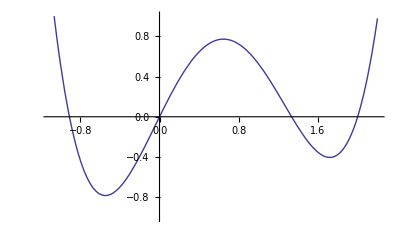

```mathematica
Plot[qf[x],{x,-1.1,2.2},PlotRange->{-1,1},AspectRatio->2/3.3]
```

```mathematica
showinvimg[qf,-1.1,2.2,-.3,.75,.05,-1,1,4/8.4]
```

#### Quintic

```mathematica
ff[x_]:=-.5+.5x+.2x^2-.19x^3-.015x^4+.01x^5
```

```mathematica
Manipulate[setup[ff,a,b,x],{{a,-1},-2,2,.05,Appearance->{"Labeled","Open"}},{{b,1},-2,2,.05,Appearance->{"Labeled","Open"}}]
```

```mathematica
Manipulate[setup[ff,a,b,x]//TreeForm,{{a,-1},-2,2,.05,Appearance->{"Labeled","Open"}},{{b,1},-2,2,.05,Appearance->{"Labeled","Open"}}]
```

```mathematica
showinvimg[ff,-4.1,4.3,-1.4,1,.05,-2,2,4/8.4]
```

#### Log

```mathematica
Manipulate[setup[Log,a,b,x],{{a,-1},.5,1.3,.05,Appearance->{"Labeled","Open"}},{{b,1},-2,2,.05,Appearance->{"Labeled","Open"}}]
```

```mathematica
showinvimg[Log,.001,3,.5,1.3,.05,-1.5,1.5,3/3]
```

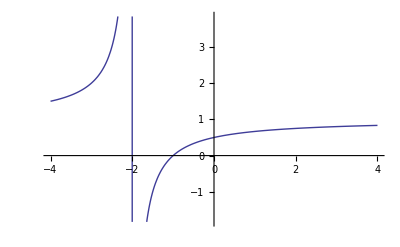

```mathematica
Plot[(x+1)/(x+2),{x,-4,4}]
```

```mathematica
steep[x_]:=2x
```

```mathematica
showinvimg[steep,-1,1,-.5,.5,.05,-2,2,4/2]
```

```mathematica
easy[x_]:=x/2
```

```mathematica
showinvimg[easy,-2,2,-.7,.5,.05,-1,1,1/2]
```